Hamiltonian Simulation H=Z

§4.7 Simulation of quantum systems, Nielsen & Chuang

Notebook: Óscar Amaro, July 2021 @ GoLP-EPP
Contact: oscar.amaro@tecnico.ulisboa.pt

Introduction
Quantum circuit for simulating the Hamiltonian H=⊗Z for time Δt.
Get the Quantum Mathematica package at https://homepage.cem.itesm.mx/lgomez/

```mathematica
(* import package *)
Needs["Quantum`Computing`"];
```

## n=1

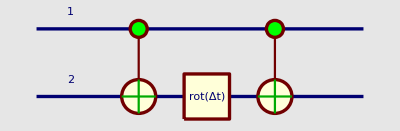

U1={{ⅇ^(-ⅈ Δt),0,0,0},{0,ⅇ^(-ⅈ Δt),0,0},{0,0,ⅇ^(ⅈ Δt),0},{0,0,0,ⅇ^(ⅈ Δt)}}

U2={{ⅇ^(-ⅈ Δt),0,0,0},{0,ⅇ^(ⅈ Δt),0,0},{0,0,ⅇ^(ⅈ Δt),0},{0,0,0,ⅇ^(-ⅈ Δt)}}

ψ={a[0],0,a[1],0}

{1,1,1,1}

```mathematica
Clear[Δt,I2,Z,RZ,U1,U2,rot,psi]
I2=PauliMatrix[0];
Z=PauliMatrix[3];

(* direct method *)
U1=MatrixExp[-I KroneckerProduct[Z,I2]Δt];

(* define Rz rotation *)
SetQuantumGate[rot,1,
Function[{q1},
Function[{Δt},
ⅇ^(-ⅈ Δt)|Subscript[0, OverHat[q1]]⟩·⟨Subscript[0, OverHat[q1]]|+ⅇ^(+ⅈ Δt)|Subscript[1, OverHat[q1]]⟩·⟨Subscript[1, OverHat[q1]]| ] ] ];
QuantumTableForm[Subscript[rot, OverHat[1]][Δt]];
QuantumMatrixForm[Subscript[rot, OverHat[1]][Δt]];
QuantumMatrixForm[(𝒞^{OverHat[3]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]];

(* build circuit *)
circ=(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]]·Subscript[rot, OverHat[2]][Δt]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[2]]];
(* plot *)
QuantumPlot[circ]
U2=QuantumMatrix[circ];
(* compare unitaries *)
Print["U1=",U1]
Print["U2=",U2]
(* define test ket. We are only interested on the effect of the operators on an arbitrary ket (where the ancilla is supposed to start as 0) *)
psi=ArrayFlatten[KroneckerProduct[{a[0],a[1]},{1,0}],1];
Print["ψ=",psi]
(* the non-zero entries of this ket will select the relevant entries of the operators *)
(* because of zero entries in U1,U2, we need to add ϵ to the operators and then take the limit ϵ->0 *)
Limit[(U1.psi+ϵ)/(U2.psi+ϵ),ϵ->0]
(* the resulting kets are the same *)
```

## n=2

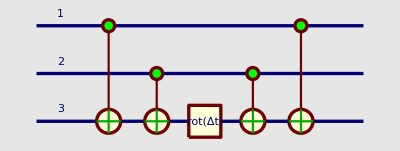

{1,1,1,1,1,1,1,1}

```mathematica
Clear[Δt,I2,Z,RZ,U1,U2,rot,psi]
I2=PauliMatrix[0];
Z=PauliMatrix[3];

(* direct method *)
U1=MatrixExp[-I KroneckerProduct[Z,Z,I2]Δt];

(* define Rz rotation *)
SetQuantumGate[rot,1,
Function[{q1},
Function[{Δt},
ⅇ^(-ⅈ Δt)|Subscript[0, OverHat[q1]]⟩·⟨Subscript[0, OverHat[q1]]|+ⅇ^(+ⅈ Δt)|Subscript[1, OverHat[q1]]⟩·⟨Subscript[1, OverHat[q1]]| ] ] ];
QuantumTableForm[Subscript[rot, OverHat[1]][Δt]];
QuantumMatrixForm[Subscript[rot, OverHat[1]][Δt]];
QuantumMatrixForm[(𝒞^{OverHat[3]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]];

(* build circuit *)
circ=(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·Subscript[rot, OverHat[3]][Δt]·(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[3]]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[3]]];
(* plot *)
QuantumPlot[circ]
U2=QuantumMatrix[circ];
(* compare unitaries *)
psi=ArrayFlatten[KroneckerProduct[{a[0],a[1]},{a[2],a[3]},{1,0}],1];
Limit[(U1.psi+ϵ)/(U2.psi+ϵ),ϵ->0]
```

## n=3

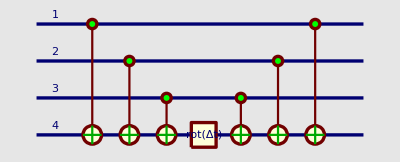

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Clear[Δt,I2,Z,RZ,U1,U2,psi]
I2=PauliMatrix[0];
Z=PauliMatrix[3];

(* direct method *)
U1=MatrixExp[-I KroneckerProduct[Z,Z,Z,I2]Δt];

(* define Rz rotation *)
SetQuantumGate[RZ,1,
Function[{q1},
Function[{Δt},
ⅇ^(-ⅈ Δt)|Subscript[0, OverHat[q1]]⟩·⟨Subscript[0, OverHat[q1]]|+ⅇ^(+ⅈ Δt)|Subscript[1, OverHat[q1]]⟩·⟨Subscript[1, OverHat[q1]]| ] ] ];
QuantumTableForm[Subscript[rot, OverHat[1]][Δt]];
QuantumMatrixForm[Subscript[rot, OverHat[1]][Δt]];
QuantumMatrixForm[(𝒞^{OverHat[3]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]];

(* build circuit *)
circ=(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]·(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]·(𝒞^{OverHat[3]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]·Subscript[rot, OverHat[4]][Δt]·(𝒞^{OverHat[3]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]·(𝒞^{OverHat[2]})[Subscript[𝒩𝒪𝒯, OverHat[4]]]·(𝒞^{OverHat[1]})[Subscript[𝒩𝒪𝒯, OverHat[4]]];

(* plot *)
QuantumPlot[circ]
U2=QuantumMatrix[circ];
(* compare unitaries *)
psi=ArrayFlatten[KroneckerProduct[{a[0],a[1]},{a[2],a[3]},{a[4],a[5]},{1,0}],1];
Limit[(U1.psi+ϵ)/(U2.psi+ϵ),ϵ->0]
```